# Why the geometric average?

The geometric average is calculated as  ((1+r_1)(1+r_2)...(1+r_3))^(1/n)-1

The arithmetic average is calculated as (r_1+r_2+...+r_n)/n

Example
Consider a stock whose returns are +5%, +10%, -10%, -5%, +1%

Then the geometric average is  ((1+5/100)(1+10/100)(1+-10/100)(1+-5/100)(1+1/100))^(1/5)-1 which is roughly -0.05%

And the arithmetic average is (5+10-10-5+1)/5or 0.2%

So, the geometric average is negative while arithmetic average (from here on referred to as the mean) is positive. Assuming the distribution is going to maintain itself over n periods, should we invest in this asset? 

Running a small simulation
Let’s run a simulation with the following rules:
1. We start with a wealth of 1. 
2. We invest all our returns on the stock.
3. On each turn we randomly pick a return R_i from +5%, +10%, -10%, -5%, +1% and increase our wealth accordingly.
4. We repeat many times.

The following graph shows the wealth of the player over time.

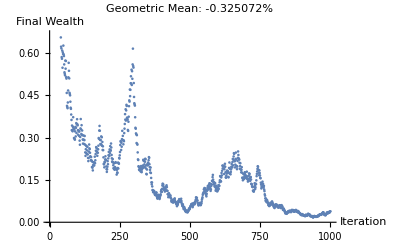

```mathematica
With[
{
values = RandomVariate[EmpiricalDistribution[{1+5./100, 1+10./100,1+-10./100,1+-5./100,1-1./100 }],1000]
},
FoldList[#1*#2&,1,values]//
ListPlot[#,{
PlotLabel->"Geometric Mean: "<>ToString[(GeometricMean[values]-1)*100]<>"%",
AxesLabel->{"Iteration", "Final Wealth"}
}]&
]
```

Given enough time, a negative edge (negative geometric mean) will eventually lead to bankruptcy.

Let’s now run the same simulation but with a distribution that has a positive geometric mean.

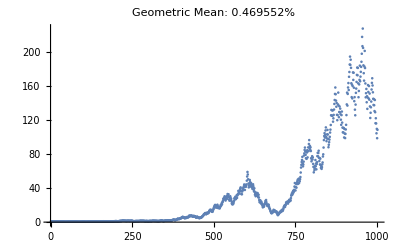

```mathematica
With[
{
values = RandomVariate[EmpiricalDistribution[{1+5./100, 1+10./100,1+-10./100,1+-5./100,1+3.3/100 }],1000]
},
FoldList[#1*#2&,1,values]//ListPlot[#,{PlotLabel->"Geometric Mean: "<>ToString[(GeometricMean[values]-1)*100]<>"%"}]&
]
```

Now we see the reverse result. A small, but positive edge will eventually lead us to infinite wealth. Do take notice of the scales of both of these graphs.

Including Probabilities
Another way of calculating the Geometric Mean is by looking at the probabilities. Going back to our example, given the following distribution: +5%, +10%, -10%, -5%, +1% we can encode this as follows:

P(S=+5%) = 1/5
P(S=+10%) = 1/5
P(S=-10%) = 1/5
P(S=-5%) = 1/5
P(S=+1%) = 1/5

Each row reads “the probability of the stock having a return of X equals 1/5”. 

The geometric mean can be calculated as follows:

Geometric Mean=(1+r_1)^(P(S=r_1)) (1+r_2)^(P(S=r_2))... (1+r_n)^(P(S=r_n))-1 

Applying to our example we get 

1.05^(1/5)1.10^(1/5)0.90^(1/5)0.95^(1/5)1.01^(1/5) -1, which is roughly -0.05%

Conclusions
I hope this small article convinced you of why the geometric mean is a better way of comparing distribution of assets. A few important characteristics to keep in mind:

How to calculate
There are two ways:

 (1+r_1)^(P(S=r_1)) (1+r_2)^(P(S=r_2))... (1+r_n)^(P(S=r_n))-1

or

((1+r_n)(1+r_n)...(1+r_n))^(1/n)-1

Bankruptcy Protection
If the distribution contains a -1, or in other words if there is a possibility of bankruptcy, the geometric mean will be 0. Just consider what would happen if r_i=-1 in the formula ((1+r_n)(1+r_n)...(1-1)...(1+r_n))^(1/n).

Wild Swings
Even if the geometric mean is positive, there can be very long paths leading downwards.

The Law of Large Numbers
A small but positive edge will over time increase your wealth. The converse is also true: a small but negative edge over time will lead you to bankruptcy, which means that it is very important that your estimation of the geometric mean doesn’t suddenly turn negative.